```mathematica
(*define dispersion function*)
t=1.0;
a=1.0;

E1[kx_,ky_]:=2 t;

E2[kx_,ky_]:=t (-1+Sqrt[3+2 Cos[2 a ky]+2 Cos[2 a (-0.5 kx+ky Sqrt[3]/2)]+2 Cos[2 a (-0.5 kx+ky 0.5 (2+Sqrt[3]))]]);

E3[kx_,ky_]:=t (-1-Sqrt[3+2 Cos[2 a ky]+2 Cos[2 a (-0.5 kx+ky Sqrt[3]/2)]+2 Cos[2 a (-0.5 kx+ky 0.5 (2+Sqrt[3]))]]);
```

```mathematica
(*grid resolution*)
nk=200; 
kxVals=Subdivide[-Pi,Pi,nk];
kyVals=Subdivide[-Pi,Pi,nk];

(*numerically solved, essentially want to input value as probability distribution, try as normal distribution *)
energies=Reap[For[i=1,i<=Length[kxVals],i++,For[j=1,j<=Length[kyVals],j++,
kx=kxVals[[i]];
ky=kyVals[[j]];
vals={E2[kx,ky],E3[kx,ky]};
Do[If[-4t<=x<=2t,Sow[x]],{x,vals}];
]]
][[2,1]];
```

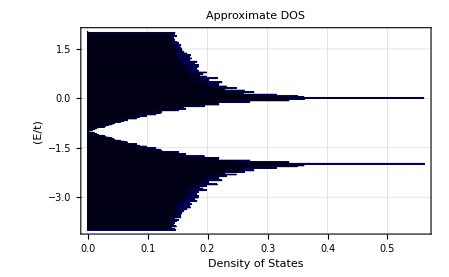

```mathematica
(*histogram*)
hist= Histogram[energies,{0.025},"PDF",ChartStyle->Directive[Blue],Frame->True,FrameLabel->{"Density of States","(E/t)"},PlotLabel->"Approximate DOS", GridLines->Automatic, BarOrigin->Left]
```

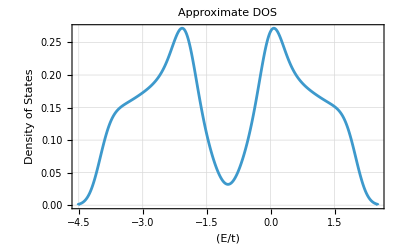

```mathematica
(*smoothened graph, why its going past limits histogram goes to? think comes form the kernalling discrepancy*)
SmoHist = SmoothHistogram[energies,Automatic,"PDF",Frame->True,FrameLabel->{"(E/t)","Density of States"},PlotLabel->"Approximate DOS", GridLines->Automatic]
```

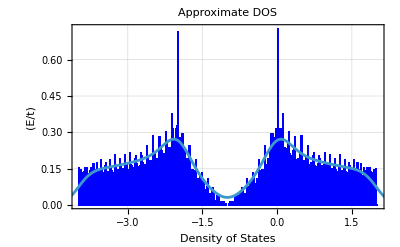

```mathematica
Show[Histogram[energies,{0.025},"ProbabilityDensity",ChartStyle->Directive[Blue],Frame->True,FrameLabel->{"E/t","Density of states"},PlotLabel->"Approximate DOS", GridLines->Automatic],SmoHist]
```

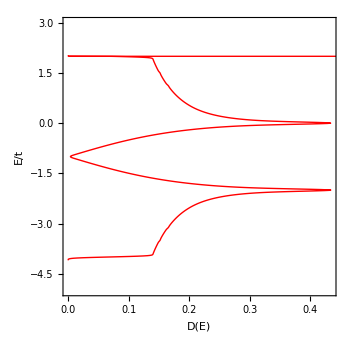

```mathematica
(*parameters and evalues*)

Clear["Global`*"]

(*parameters*)
t=1.0;
a=1.0;

(*bands*)
E1[kx_,ky_]:=2 t;

E2[kx_,ky_]:=t (-1+Sqrt[3+2 Cos[2 a ky]+2 Cos[2 a (-kx/2+Sqrt[3] ky/2)]+2 Cos[2 a (-kx/2+(2+Sqrt[3]) ky/2)]]);

E3[kx_,ky_]:=t (-1-Sqrt[3+2 Cos[2 a ky]+2 Cos[2 a (-kx/2+Sqrt[3] ky/2)]+2 Cos[2 a (-kx/2+(2+Sqrt[3]) ky/2)]]);

(*k-grid*)
nk=600;
kxVals=Subdivide[-Pi,Pi,nk];
kyVals=Subdivide[-Pi,Pi,nk];

(*sample all bands*)
energiesAll=Flatten[Table[{E1[kx,ky],E2[kx,ky],E3[kx,ky]},{kx,kxVals},{ky,kyVals}],2];

(*sample only dispersive bands if you want the smooth orange-shaped DOS*)
energiesDisp=Flatten[Table[{E2[kx,ky],E3[kx,ky]},{kx,kxVals},{ky,kyVals}],2];

(*Gaussian broadening*)
η=0.025;
gauss[x_]:=Exp[-x^2/(2 η^2)]/(Sqrt[2 Pi] η);

Emin=-4.1;
Emax=2.03;
eVals=Subdivide[Emin,Emax,800];

(*DOS*)
dosDisp=Mean[gauss[eVals-#]&/@energiesDisp];

(*remove Gaussian tail above the flat band*)dosDispClipped=MapThread[If[#2<=2,#1,0]&,{dosDisp,eVals}];

(*optional:set tiny values to zero for cleaner presentation*)
cutoff=5*10^-4;
dosClean=dosDispClipped/. x_/;x<cutoff->0;

dispData=Transpose[{dosClean,eVals}];

xmax=Max[dispData[[All,1]]];

Show[ListLinePlot[dispData,PlotStyle->{Thick,Red},Frame->True,Axes->False,FrameLabel->{Style["D(E)",Bold],Style["E/t",Bold]},PlotRange->{{0,All},{-5,3}},AspectRatio->1,ImageSize->350],Graphics[{Thick,Red,Line[{{0,1.9999},{Max[dispData[[All,1]]]*1.05,2}}]}]]
```

```mathematica
(*define eigenvlues for DP and VHs investigation*)
t=1.0;
a=1.0;

E1[kx_,ky_]:=2 t;

E2[kx_,ky_]:=t (-1+Sqrt[3+2 Cos[2 a ky]+2 Cos[2 a (-0.5 kx+ky Sqrt[3]/2)]+2 Cos[2 a (-0.5 kx+ky 0.5 (2+Sqrt[3]))]]);

E3[kx_,ky_]:=t (-1-Sqrt[3+2 Cos[2 a ky]+2 Cos[2 a (-0.5 kx+ky Sqrt[3]/2)]+2 Cos[2 a (-0.5 kx+ky 0.5 (2+Sqrt[3]))]]);
```

```mathematica
(*define differential equations for VHs*)
dE2dky[kx_,ky_] :=D[E2[kx,ky],ky] ;

dE2dkx[kx_,ky_] :=D[E2[kx,ky],kx] ;
```

```mathematica
(*solving equations numerically with guesses*)
sol1=FindRoot[{dE2dkx[kx,ky]==0,dE2dky[kx,ky]==0},{{kx,3},{ky,0}}]
sol2=FindRoot[{dE2dkx[kx,ky]==0,dE2dky[kx,ky]==0},{{kx,-3},{ky,0}}]
sol3=FindRoot[{dE2dkx[kx,ky]==0,dE2dky[kx,ky]==0},{{kx,0},{ky,1}}]
```

{kx→3.14159,ky→-1.61949×10^-19}

{kx→-3.14159,ky→1.61949×10^-19}

{kx→21.5703,ky→1.5708}

```mathematica
(*solve by guesses*)
guesses={{3,0},{-3,0},{0,1},{0,-1},{2,1},{-2,-1}};

sols=Table[Quiet@FindRoot[{dE2dkx[kx,ky]==0,dE2dky[kx,ky]==0},{{kx,g[[1]]},{ky,g[[2]]}}],{g,guesses}];

pts=({kx,ky}/. sols)//N ; 
pts=DeleteDuplicates[pts,Norm[#1-#2]<10^-5&]
```

{{3.14159,-1.61949×10^-19},{-3.14159,1.61949×10^-19},{21.5703,1.5708},{-21.5703,-1.5708},{-2.7207,-1.5708},{2.7207,1.5708}}

```mathematica
(* classifying points with hessian *)
Hs={{D[E2[x,y],{x,2}],D[E2[x,y],x,y]},{D[E2[x,y],y,x],D[E2[x,y],{y,2}]}};

Table[{p,Det[Hs/. {x->p[[1]],y->p[[2]]}]//N},{p,pts}]
```

{{{3.14159,-1.61949×10^-19},-4.},{{-3.14159,1.61949×10^-19},-4.},{{21.5703,1.5708},-4.},{{-21.5703,-1.5708},-4.},{{-2.7207,-1.5708},-4.},{{2.7207,1.5708},-4.}}

```mathematica
(*same method for E3*)
dE3dky[kx_,ky_] := D[E3[kx,ky],ky] ;

dE3dkx[kx_,ky_] :=D[E3[kx,ky],kx]  ;

guesses={{3,0},{-3,0},{0,1},{0,-1},{2,1},{-2,-1}};

sols=Table[Quiet@FindRoot[{dE3dkx[kx,ky]==0,dE3dky[kx,ky]==0},{{kx,g[[1]]},{ky,g[[2]]}}],{g,guesses}];

pts=({kx,ky}/. sols)//N ; 
pts=DeleteDuplicates[pts,Norm[#1-#2]<10^-5&]
```

{{3.14159,-1.61949×10^-19},{-3.14159,1.61949×10^-19},{21.5703,1.5708},{-21.5703,-1.5708},{-2.7207,-1.5708},{2.7207,1.5708}}

```mathematica
(*numerically finding dirac point*)


ClearAll[g,gap2,diracFromSeed];

a=1;t=1;

g[kx_?NumericQ,ky_?NumericQ]:=N[E2[kx,ky]-E3[kx,ky],50];
gap2[kx_?NumericQ,ky_?NumericQ]:=g[kx,ky]^2;

diracFromSeed[{kx0_?NumericQ,ky0_?NumericQ}]:=Module[{sol},sol=FindMinimum[gap2[kx,ky],{{kx,kx0},{ky,ky0}}];
{kx,ky}/. Last[sol]];

diracFromSeed[{2 Pi/3,2 Pi/3}]
```

{-0.280596,1.0472}

```mathematica
k0=diracFromSeed[{2 Pi/3,2 Pi/3}]
N[g[k0[[1]],k0[[2]]]]
```

{-0.280596,1.0472}

1.3328×10^-7

```mathematica
(* plotting flatband over parametrised lines *)
```

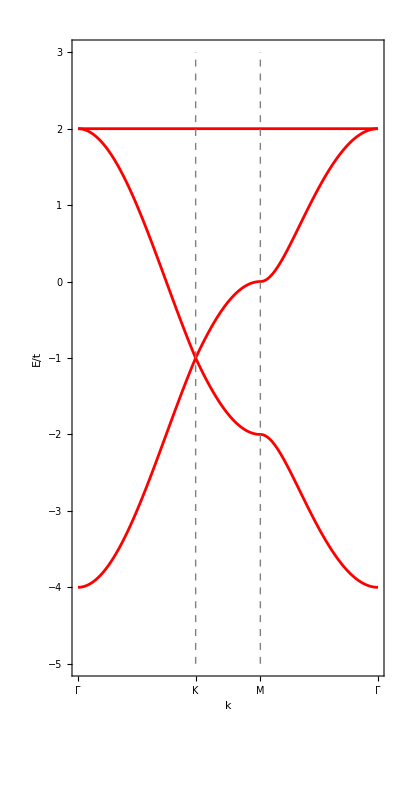

```mathematica
Clear["Global`*"]

(*Parameters*)
a=1.0;
tHop=1.0;
kxK=-0.280596;
kyK=1.0472;
kxM=2.7207;
kyM=1.5708;

(*Γ->K*)
k1[s_]:={s kxK,s kyK};
(*K->M*)
k2[s_]:={kxK+s (kxM-kxK),kyK+s (kyM-kyK)};
(*M->Γ*)
k3[s_]:={kxM (1-s),kyM (1-s)};

(*Arc-length positions for x-axis*)
L1=1.0;
L2=0.55;
L3=1.0;

x1[s_]:=s L1;
x2[s_]:=L1+s L2;
x3[s_]:=L1+L2+s L3;

(*Kagome dispersion*)
Eflat[kx_,ky_]:=2 tHop;
Eplus[kx_,ky_]:=tHop (-1+Sqrt[3+2 Cos[2 a ky]+2 Cos[2 a (-0.5 kx+ky Sqrt[3]/2)]+2 Cos[2 a (-0.5 kx+ky 0.5 (2+Sqrt[3]))]]);

Eminus[kx_,ky_]:=tHop (-1-Sqrt[3+2 Cos[2 a ky]+2 Cos[2 a (-0.5 kx+ky Sqrt[3]/2)]+2 Cos[2 a (-0.5 kx+ky 0.5 (2+Sqrt[3]))]]);


(*Sample points along each segment*)
n=300;

seg1=Table[With[{k=k1[s]},{x1[s],Eflat@@k,Eplus@@k,Eminus@@k}],{s,0,1,1.0/n}];

seg2=Table[With[{k=k2[s]},{x2[s],Eflat@@k,Eplus@@k,Eminus@@k}],{s,0,1,1.0/n}];

seg3=Table[With[{k=k3[s]},{x3[s],Eflat@@k,Eplus@@k,Eminus@@k}],{s,0,1,1.0/n}];

data=Join[seg1,seg2,seg3] ;

(*Vertical separator positions*)
xK=L1;
xM=L1+L2;
xG2=L1+L2+L3;

ListLinePlot[{data[[All,{1,2}]],data[[All,{1,3}]],data[[All,{1,4}]]},Frame->True,Axes->False,PlotStyle->Red,FrameLabel->{Style["k",Bold],Style["E/t",Bold]},PlotRange->{{0,xG2},{-5,3}},Epilog->{Dashed,Gray,Line[{{xK,-5},{xK,3}}],Line[{{xM,-5},{xM,3}}]},FrameTicks->{{Automatic,None},{{{0,"Γ"},{xK,"K"},{xM,"M"},{xG2,"Γ"}},None}},AspectRatio->2]
```

```mathematica
ListLinePlot[{data[[All,{1,2}]],data[[All,{1,3}]],data[[All,{1,4}]]},Frame->True,Axes->False,PlotStyle->Red,FrameLabel->{"","E/t"},PlotRange->{{0,xG2},{-5,3}},Epilog->{Dashed,Gray,Line[{{xK,-5},{xK,3}}],Line[{{xM,-5},{xM,3}}]},FrameTicks->{{Automatic,None},{{{0,"Γ"},{xK,"K"},{xM,"M"},{xG2,"Γ"}},None}},AspectRatio->2]
```

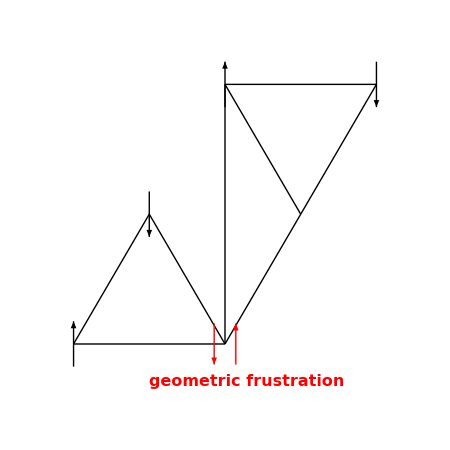

```mathematica
Clear["Global`*"]

spinArrowAt[pt_,v_,len_:0.42,col_:Black]:=Module[{u},u=Normalize[v];
{col,Thick,Arrowheads[0.05],Arrow[{pt-(len/2) u,pt+(len/2) u}]}];

pts={{0,0},{1.4,0},{0.7,1.2},(*upper triangle*){2.1,1.2},{1.4,2.4},{2.8,2.4}     (*neighboring kagome-style motif*)};

bonds={{pts[[1]],pts[[2]]},{pts[[2]],pts[[3]]},{pts[[3]],pts[[1]]},{pts[[2]],pts[[4]]},{pts[[4]],pts[[5]]},{pts[[5]],pts[[2]]},{pts[[4]],pts[[6]]},{pts[[5]],pts[[6]]}};

Graphics[{Black,Thick,Line/@bonds,(*spins arranged to suggest antiferromagnetic incompatibility*)spinArrowAt[pts[[1]],{0,1}],spinArrowAt[pts[[3]],{0,-1}],spinArrowAt[pts[[5]],{0,1}],spinArrowAt[pts[[6]],{0,-1}],(*frustrated shared site*)Red,spinArrowAt[pts[[2]]+{0.1,0},{0,1},0.38,Red],spinArrowAt[pts[[2]]-{0.1,0},{0,-1},0.38,Red],Text[Style["geometric frustration",16,Red,Bold,FontFamily->"Helvetica"],{1.6,-0.35}]},PlotRange->{{-0.3,3.1},{-0.6,2.8}},ImageSize->450,Background->White]
```

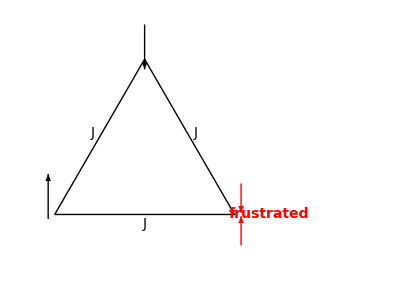

```mathematica
Clear["Global`*"]

(*triangle vertices*)
p1={0,0};
p2={2.2,0};
p3={1.1,1.9};

(*arrow helper*)
spinArrow[pos_,dir_,len_:0.55,col_:Black]:={col,Thick,Arrowheads[0.05],Arrow[{pos-{0,len/2} dir,pos+{0,len/2} dir}]};

Graphics[{(*triangle*)Black,Thick,Line[{p1,p2,p3,p1}],(*localized spins on the three sites*)spinArrow[p1+{-0.08,0.22},1],(*left spin up*)spinArrow[p3+{0,0.15},-1],(*top spin down*)(*frustrated right site:two possible directions shown*)Red,Thick,Arrowheads[0.05],Arrow[{p2+{0.08,0.38},p2+{0.08,0.02}}],(*down option*)Arrow[{p2+{0.08,-0.38},p2+{0.08,-0.02}}],(*up option*)(*frustration marker*)Text[Style["frustrated",14,Red,Bold,FontFamily->"Helvetica"],p2+{0.42,0}],(*optional bond labels/interaction hints*)Text[Style["J",14,Black],(p1+p2)/2+{0,-0.12}],Text[Style["J",14,Black],(p1+p3)/2+{-0.08,0.05}],Text[Style["J",14,Black],(p2+p3)/2+{0.08,0.05}]},PlotRange->{{-0.2,4.0},{-0.6,2.3}},ImageSize->420,Background->White]
```

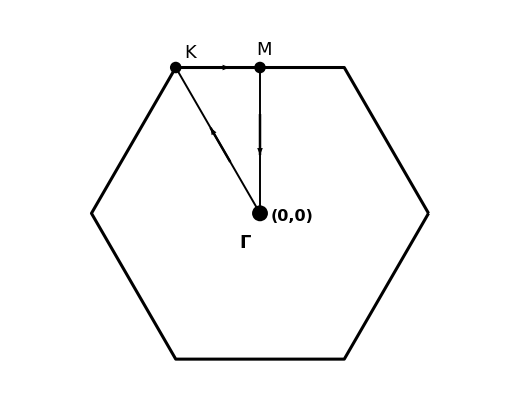

```mathematica
Clear["Global`*"]

(*---regular hexagon centered at Gamma---*)
R=1.15;
hex=Table[R {Cos[n Pi/3],Sin[n Pi/3]},{n,0,5}];

(*---high-symmetry points---*)
Γ={0,0};
M=Mean[{hex[[2]],hex[[3]]}];   (*midpoint of top edge*)
K=hex[[3]];                     (*top-right corner*)

(*helper:arrow centered on a segment*)
midArrow[p1_,p2_,back_:0.16,front_:0.10]:=Module[{u,mid},u=Normalize[p2-p1];
mid=(p1+p2)/2;
Arrow[{mid-back u,mid+front u}]];

Graphics[{(*hexagon*){Black,AbsoluteThickness[2.2],Line[Append[hex,First[hex]]]},(*straight guide lines between points*){Black,AbsoluteThickness[1.4],Line[{Γ,K}],Line[{K,M}],Line[{M,Γ}]},(*arrows placed halfway along each segment*){Black,AbsoluteThickness[1.8],Arrowheads[0.04],midArrow[Γ,K,0.17,0.10],midArrow[K,M,0.14,0.08],midArrow[M,Γ,0.18,0.10]},(*point markers*){Black,PointSize[0.016],Point/@{M,K}},{Black,PointSize[0.022],Point[Γ]},(*labels*)Text[Style["M",18,Italic,FontFamily->"Times"],M+{0.03,0.12}],Text[Style["K",18,Italic,FontFamily->"Times"],K+{0.10,0.1}],Text[Style["Γ",18,Bold,FontFamily->"Times"],Γ+{-0.10,-0.20}],Text[Style["(0,0)",16,Bold,FontFamily->"Times"],Γ+{0.22,-0.02}]},PlotRange->{{-1.45,1.45},{-1.10,1.20}},ImageSize->520,Background->White]
```

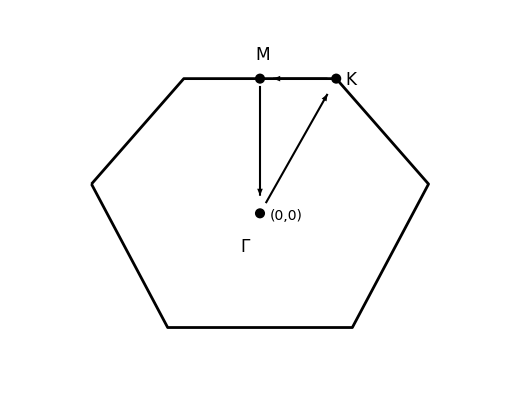

```mathematica
Clear["Global`*"]

hex={{-1.15,0.20},{-0.52,0.92},{0.52,0.92},{1.15,0.20},{0.63,-0.78},{-0.63,-0.78}};

Γ={0,0};
M={0,0.92};
K={0.52,0.92};

shortArrow[p1_,p2_,s1_:0.06,s2_:0.10]:=Module[{v=p2-p1,u},u=Normalize[v];
Arrow[{p1+s1 u,p2-s2 u}]];

Graphics[{{Black,AbsoluteThickness[2.0],Line[Append[hex,First[hex]]]},{Black,AbsoluteThickness[1.5],Arrowheads[0.035],shortArrow[Γ,K,0.08,0.12],shortArrow[K,M,0.06,0.09],shortArrow[M,Γ,0.05,0.12]},{Black,PointSize[0.014],Point/@{Γ,M,K}},Text[Style["M",17,Italic,FontFamily->"Times"],M+{0.02,0.16}],Text[Style["K",17,Italic,FontFamily->"Times"],K+{0.10,-0.01}],Text[Style["Γ",17,Italic,FontFamily->"Times"],Γ+{-0.10,-0.23}],Text[Style["(0,0)",14,FontFamily->"Times"],Γ+{0.18,-0.02}]},PlotRange->{{-1.45,1.45},{-1.10,1.20}},ImageSize->520,Background->White]
```

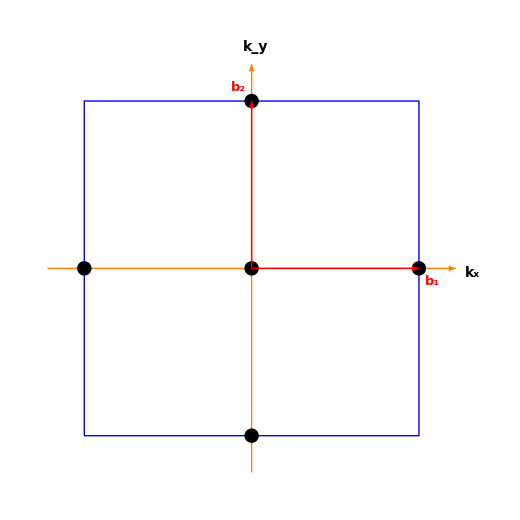

```mathematica
ClearAll["Global`*"];

a=1;
p=Pi/a;

b1={2 Pi/a,0};
b2={0,2 Pi/a};

Graphics[{(*axes*){Orange,Thick,Arrow[{{-1.22 p,0},{1.22 p,0}}],Arrow[{{0,-1.22 p},{0,1.22 p}}]},Text[Style[Subscript["k","x"],14,Bold],{1.32 p,-0.08}],Text[Style[Subscript["k","y"],14,Bold],{0.08,1.32 p}],(*Brillouin zone*){Blue,Thick,Line[{{-p,-p},{p,-p},{p,p},{-p,p},{-p,-p}}]},(*points*){Black,PointSize[0.02],Point[{0,0}],Point[{p,0}],Point[{-p,0}],Point[{0,p}],Point[{0,-p}]},(*reciprocal lattice vectors*){Red,Thick,Arrow[{{0,0},0.5 b1}],Arrow[{{0,0},0.5 b2}]},(*vector labels:close to arrow tips*)Text[Style[Subscript["b","1"],13,Bold,Red],0.5 b1+{0.08 p,-0.08 p}],Text[Style[Subscript["b","2"],13,Bold,Red],0.5 b2+{-0.08 p,0.08 p}],(*coordinate labels:spaced cleanly*)PlotRange->{{-1.5 p,1.6 p},{-1.5 p,1.5 p}},ImageSize->520,Axes->False,Background->White}]
```

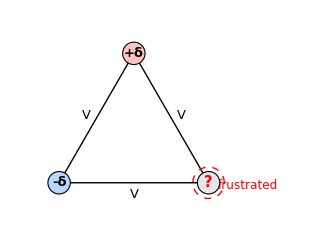

```mathematica
ClearAll["Global`*"];

r1={0,0};
r2={1,0};
r3={0.5,Sqrt[3]/2};

m12=(r1+r2)/2;
m23=(r2+r3)/2;
m31=(r3+r1)/2;

fig=Graphics[{Thick,Black,Line[{r1,r2,r3,r1}],Text[Style["V",13],m12+{0,-0.08}],Text[Style["V",13],m23+{0.07,0.02}],Text[Style["V",13],m31+{-0.07,0.02}],EdgeForm[{Black,Thick}],{RGBColor[0.72,0.84,1.0],Disk[r1,0.075]},Text[Style["-δ",13,Bold],r1],{RGBColor[1.0,0.76,0.76],Disk[r3,0.075]},Text[Style["+δ",13,Bold],r3],{GrayLevel[0.9],Disk[r2,0.075]},{Red,Thick,Dashed,Circle[r2,0.105]},Text[Style["?",15,Bold,Red],r2],Text[Style["frustrated",12,Red],r2+{0.26,-0.02}]},PlotRange->{{-0.2,1.55},{-0.2,1.08}},ImageSize->320];
fig
```